```mathematica
ClearAll[h,F]
f[r_]=1;

Psi1[r_,q_]=(C[1]/r+r C[2]+r^3 C[4]+r C[3] Log[r])Sin[q];

DPsi1[r_,q_]=D[Psi1[r,q],r];
om1[r_,q_]=-1/r D[r DPsi1[r,q],r]-1/r^2 D[Psi1[r,q],{q,2}];
Dom1[r_,q_]=D[om1[r,q],r];
Psi2[r_,q_]=(C[5]/r+r C[6]+r^3 C[8]+r C[7] Log[r])Sin[q];

DPsi2[r_,q_]=D[Psi2[r,q],r];
om2[r_,q_]=-1/r D[r DPsi2[r,q],r]-1/r^2 D[Psi2[r,q],{q,2}];
Dom2[r_,q_]=D[om2[r,q],r];
Vq1[R_,q_]=-D[Psi1[R,q],R];
Vq2[R_,q_]=-D[Psi2[R,q],R];

ds2=Solve[{Psi1[r0,Pi/2]==0,DPsi1[r0,Pi/2]==0,Psi1[(h+r0)/2,Pi/2]==Psi2[(h+r0)/2,Pi/2],om1[(h+r0)/2,Pi/2]==om2[(h+r0)/2,Pi/2],Vq1[(h+r0)/2,Pi/2]==Vq2[(h+r0)/2,Pi/2],Dom1[(h+r0)/2,Pi/2]-f[(h+r0)/2]==Dom2[(h+r0)/2,Pi/2],Dom2[h,Pi/2]==0,om2[h,Pi/2]==0},{C[1],C[2],C[3],C[4],C[5],C[6],C[7],C[8]}]
```

((C[1]/r+r C[2]+r^3 C[4]+r C[3] Log[r]) Sin[q])/r^2-(r ((2 C[1])/r^3+C[3]/r+6 r C[4]) Sin[q]+(-C[1]/r^2+C[2]+C[3]+3 r^2 C[4]+C[3] Log[r]) Sin[q])/r

```mathematica
h=5
r0=1
om1[r,fi]/.ds2[[1]]//Simplify
om2[r,fi]/.ds2[[1]]
```

5

1

((-9+r^2) Sin[fi])/(2 r)

((-4/r+1/32 r (-32+72 Log[3])) Sin[fi])/r^2-(-(8 Sin[fi])/r^2+(4/r^2+1/32 (-32+72 Log[3])) Sin[fi])/r

```mathematica
Psi1[r,q]=Psi1[r,q]/.ds2[[1]]
Psi2[r,q]=Psi2[r,q]/.ds2[[1]]
D[Psi1[r,q],q]/.q->Q1
```

(17/(16 r)-r-r^3/16+9/4 r Log[r]) Sin[q]

(-4/r+1/4 r (-4+9 Log[3])) Sin[q]

(x (17/(16 r)-r-r^3/16+9/4 r Log[r]))/(√(x^2+y^2))

```mathematica
psi[r_,fi_]:=If[r>=1&&r<=3,Psi1[r,fi]/.ds2[[1]],Psi2[r,fi]/.ds2[[1]]];
Dpsi[r_,fi_]:=If[r>=1&&r<=3,DPsi1[r,fi]/.ds2[[1]],DPsi2[r,fi]/.ds2[[1]]];
om[r_,fi_]=If[r>=1&&r<=3,om1[r,fi]/.ds2[[1]],om2[r,fi]/.ds2[[1]]];
Dom[r_,fi_]=If[r>=1&&r<=3,Dom1[r,fi]/.ds2[[1]],Dom2[r,fi]/.ds2[[1]]];
```

```mathematica
h=5;
r0=1;
r1:=√(x^2+y^2);
Q1:=ArcTan[x,y];
u1=(D[Psi1[r,q],r]/.r->r1/.q->Q1)D[r1,y]+(D[Psi1[r,q],q]/.q->Q1/.r->r1)D[Q1,y]//Simplify;
v1=-((D[Psi1[r,q],r]/.r->r1/.q->Q1)D[r1,x]+(D[Psi1[r,q],q]/.r->r1/.q->Q1)D[Q1,x])//Simplify;
u1/.x->1.1244/.y->0.14204;
v1/.x->1.1244/.y->0.14204;
Psi1[r,q]/.r->r1/.q->Q1;
om1[r,q]/.ds2[[1]]/.r->r1/.q->Q1;

u2=(D[Psi2[r,q],r]/.r->r1/.q->Q1)D[r1,y]+(D[Psi2[r,q],q]/.q->Q1/.r->r1)D[Q1,y]//Simplify
v2=-((D[Psi2[r,q],r]/.r->r1/.q->Q1)D[r1,x]+(D[Psi2[r,q],q]/.r->r1/.q->Q1)D[Q1,x])//Simplify
Psi2[r,q]/.r->r1/.q->Q1;
om2[r,q]/.ds2[[1]]
```

(x^4 (-4+9 Log[3])+2 x^2 (-8+y^2 (-4+9 Log[3]))+y^2 (16+y^2 (-4+9 Log[3])))/(4 (x^2+y^2)^2)

-(8 x y)/((x^2+y^2)^2)

((-4/r+1/4 r (-4+9 Log[3])) Sin[q])/r^2-(-(8 Sin[q])/r^2+(4/r^2+1/4 (-4+9 Log[3])) Sin[q])/r

```mathematica
nn=30;
m1=Table[0,{nn+2}];
m2=m1;
m3=m1;
m1[[1]]=m2[[1]]=m3[[1]]={"r","psi","dpsi","om","dom"};
r1=√(x^2+y^2);
Q1=ArcTan[x,y];
i=1;
r=1;
R=5;
For[alf=0,alf<=Pi,alf+=Pi/nn,
i++;
x:=r Cos[alf]//N;
y:=r Sin[alf]//N;
m1[[i]]={Floor[x,0.0001],Floor[y,0.0001],Floor[psi[r1,alf],0.0001],Floor[Dpsi[r1,alf]//N,0.0001],Floor[om[r1,alf]//N,0.0001],Floor[Dom[r1,alf]//N,0.0001]};
x:=R Cos[alf]//N;
y:=R Sin[alf]//N;
m2[[i]]={Floor[x,0.0001],Floor[y,0.0001],Floor[psi[r1,alf],0.0001],Floor[Dpsi[r1,alf]//N,0.0001],Floor[om[r1,alf]//N,0.0001],Floor[Dom[r1,alf]//N,0.0001]};

]
j=1;
For[r2=1,r2<=h,r2+=(h-1)/nn,
j++;
x:=0;
y:=r2;
(*Print[r1,Q1]*)
m3[[j]]={Floor[y,0.0001],Floor[psi[r1,Q1],0.0001],Floor[Dpsi[r1,Q1]//N,0.0001],Floor[om[r1,Q1]//N,0.0001],Floor[Dom[r1,Q1]//N,0.0001]}]
ClearAll[x,y,i,j,r,R]
(*Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text.txt",m1];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text.xls",m1,"XLS"];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text_h.txt",m2];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text_h.xls",m2,"XLS"];*)
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_mass_sil_perem.dat",m3];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_mass_sil_perem.xls",m3];
```

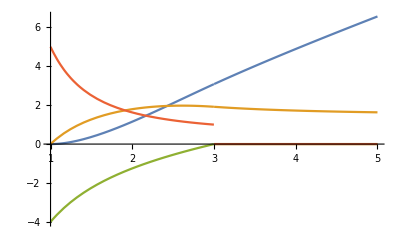

```mathematica
Plot[{psi[r,Pi/2],Dpsi[r,Pi/2],om[r,Pi/2],Dom[r,Pi/2]},{r,1,5}]
```

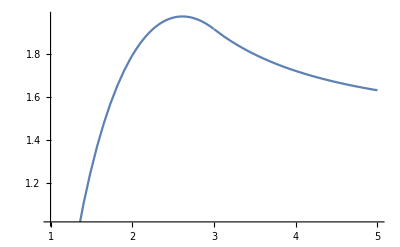

```mathematica
Plot[Dpsi[r,Pi/2],{r,1,5}]
```